```mathematica
Clear["Global`*"];
```

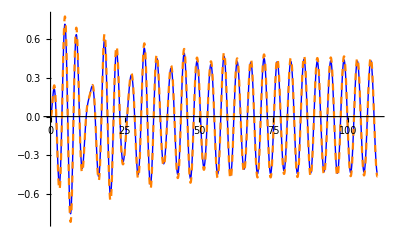

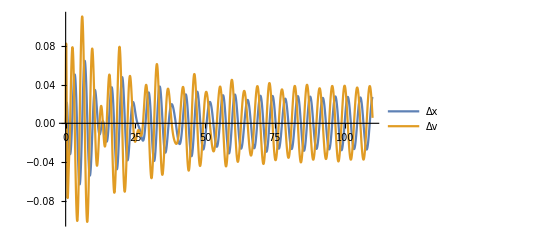

```mathematica
m=2433;k=80000;c=10000;
f=6250;omega=1.4005;k1=1025*9.8*Pi;
c0=656.3616;m0=1335.535;M=4866;
stop=110;
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Dashed]}]
Plot[Evaluate[{x1[t]-x2[t],x1'[t]-x2'[t]}/.s],{t,0,stop},PlotLegends->{"Δx","Δv"}]
```

```mathematica
targets={10,20,40,60,100};
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
Export["~/cumcm/cumcm-code/P11-paper.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}]]
```

10 | -0.190711 | -0.641009 | -0.211679 | -0.693954
20 | -0.590684 | -0.240952 | -0.634248 | -0.272776
40 | 0.285375 | 0.312972 | 0.2965 | 0.332913
60 | -0.314504 | -0.479455 | -0.331434 | -0.515728
100 | -0.0836139 | -0.604211 | -0.0840672 | -0.643001

```mathematica
Twave=1/omega
Ttargets=Table[i,{i,Range[0,40,Twave]}]
Export["~/cumcm/cumcm-code/P11.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,Ttargets}],1]]
```

0.714031

{0.,0.714031,1.42806,2.14209,2.85612,3.57015,4.28418,4.99821,5.71225,6.42628,7.14031,7.85434,8.56837,9.2824,9.99643,10.7105,11.4245,12.1385,12.8526,13.5666,14.2806,14.9946,15.7087,16.4227,17.1367,17.8508,18.5648,19.2788,19.9929,20.7069,21.4209,22.135,22.849,23.563,24.277,24.9911,25.7051,26.4191,27.1332,27.8472,28.5612,29.2753,29.9893,30.7033,31.4174,32.1314,32.8454,33.5594,34.2735,34.9875,35.7015,36.4156,37.1296,37.8436,38.5577,39.2717,39.9857}

~/cumcm/cumcm-code/P11.xlsx

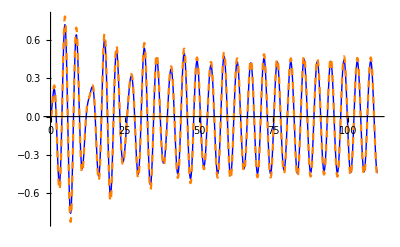

~/cumcm/cumcm-code/P12-paper.xlsx

10 | -0.191991 | -0.644618 | -0.213781 | -0.701741
20 | -0.59419 | -0.245594 | -0.640176 | -0.28171
40 | 0.282215 | 0.306276 | 0.294026 | 0.325993
60 | -0.317233 | -0.482805 | -0.335615 | -0.520822
100 | -0.0848248 | -0.605817 | -0.0862466 | -0.645578

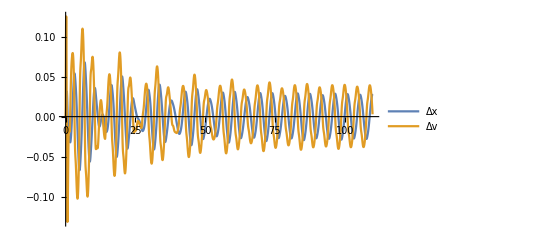

~/cumcm/cumcm-code/P12.xlsx

```mathematica
cv2[v_]:=10000*Sqrt[Abs[v]]
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Dashed]}]
Export["~/cumcm/cumcm-code/P12-paper.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}]]]
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
Plot[Evaluate[{x1[t]-x2[t],x1'[t]-x2'[t]}/.s],{t,0,stop},PlotLegends->{"Δx","Δv"}]
Export["~/cumcm/cumcm-code/P12.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,Ttargets}],1]]
```

```mathematica
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
```

```mathematica
start=510;stop=520;dim=1;
P2[cm2_]:=Sum[cm2*((x1'[i]-x2'[i])^2)*dim,{i,start,stop,dim}]/.NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
```

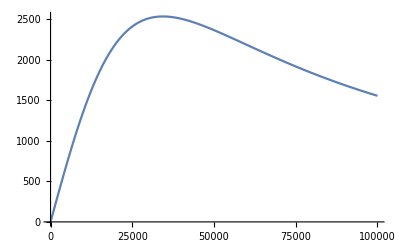

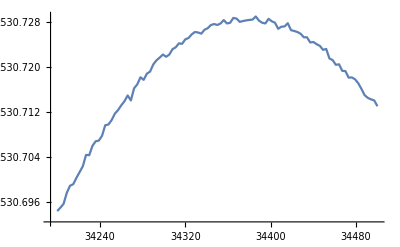

```mathematica
DrawP2[pStart_,pStop_,pStepNum_]:=ListLinePlot[Table[{i,First[P2[i]]},{i,Range[pStart,pStop,(pStop-pStart)/pStepNum]}]]
DrawP2[0,100000,100]
DrawP2[34200,34500,100]
```

```mathematica
start=510;stop=520;dim=1;
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
cmv2[v_,ck_,ce_]:=ck*Abs[v]^ce;
P22I[ck_,ce_]:=NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
P22[ck_,ce_]:=Sum[cmv2[x1'[i]-x2'[i],ck,ce+2]*dim,{i,start,stop,dim}]/.P22I[ck,ce]
```

```mathematica
CalcP22[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Table[{pe,ppk,First[P22[ppk,pe]]},{ppk,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{pe,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]
DrawP22[data_]:=ListPlot3D[Flatten[data,1]]
s=CalcP22[0,100000,8,0,1,8];
```

{0.,0.,0.} | {0.125,0.,0.} | {0.25,0.,0.} | {0.375,0.,0.} | {0.5,0.,0.} | {0.625,0.,0.} | {0.75,0.,0.} | {0.875,0.,0.} | {1.,0.,0.}
{0.,12500.,1623.99} | {0.125,12500.,1307.17} | {0.25,12500.,1035.36} | {0.375,12500.,811.778} | {0.5,12500.,632.451} | {0.625,12500.,490.881} | {0.75,12500.,380.254} | {0.875,12500.,294.401} | {1.,12500.,228.11}
{0.,25000.,2406.96} | {0.125,25000.,2140.66} | {0.25,25000.,1816.05} | {0.375,25000.,1491.34} | {0.5,25000.,1197.7} | {0.625,25000.,947.916} | {0.75,25000.,743.112} | {0.875,25000.,579.045} | {1.,25000.,449.585}
{0.,37500.,2521.14} | {0.125,37500.,2483.19} | {0.25,37500.,2276.7} | {0.375,37500.,1979.37} | {0.5,37500.,1657.05} | {0.625,37500.,1349.13} | {0.75,37500.,1077.74} | {0.875,37500.,850.132} | {1.,37500.,665.082}
{0.,50000.,2362.03} | {0.125,50000.,2528.71} | {0.25,50000.,2486.68} | {0.375,50000.,2288.55} | {0.5,50000.,1999.68} | {0.625,50000.,1682.47} | {0.75,50000.,1375.55} | {0.875,50000.,1102.08} | {1.,50000.,871.109}
{0.,62500.,2135.42} | {0.125,62500.,2438.74} | {0.25,62500.,2539.64} | {0.375,62500.,2457.79} | {0.5,62500.,2240.38} | {0.625,62500.,1946.44} | {0.75,62500.,1632.14} | {0.875,62500.,1331.46} | {1.,62500.,1065.3}
{0.,75000.,1914.64} | {0.125,75000.,2298.76} | {0.25,75000.,2507.44} | {0.375,75000.,2531.02} | {0.5,75000.,2396.64} | {0.625,75000.,2149.55} | {0.75,75000.,1846.94} | {0.875,75000.,1536.28} | {1.,75000.,1246.07}
{0.,87500.,1719.83} | {0.125,87500.,2147.2} | {0.25,87500.,2433.45} | {0.375,87500.,2543.59} | {0.5,87500.,2488.56} | {0.625,87500.,2300.15} | {0.75,87500.,2024.07} | {0.875,87500.,1715.81} | {1.,87500.,1412.39}
{0.,100000.,1553.23} | {0.125,100000.,2000.88} | {0.25,100000.,2339.96} | {0.375,100000.,2519.79} | {0.5,100000.,2534.93} | {0.625,100000.,2405.88} | {0.75,100000.,2167.93} | {0.875,100000.,1871.49} | {1.,100000.,1563.7}

-Graphics3D-

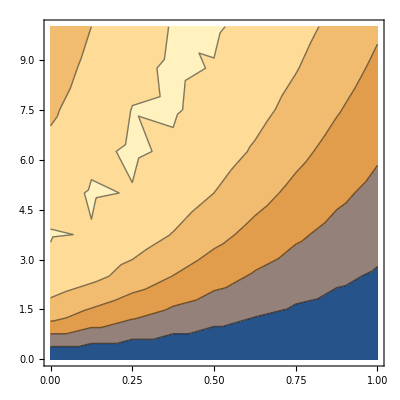

```mathematica
ss=Table[{i[[1]],i[[2]]/10000,i[[3]]},{i,Flatten[s,1]}];
Grid[N[s],Frame->All]
ListPlot3D[ss]
ListContourPlot[ss]
(*ListDensityPlot[ss]*)
```

```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=2433;
(*弹簧劲度系数*)
k=80000;
(*直线阻尼器阻尼系数*)
c=10000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*旋转阻尼器阻尼系数*)
crot=1000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=683.4558;
(*纵摇附加转动惯量*)
I0=7001.914;
(*纵摇激励力矩振幅*)
L=1690;
(*入射波浪频率*)
w=1.7152;
(*垂荡激励力振幅*)
f=3640;
(*浮子转动惯量*)
(*Ia=300*4866/(7π+(Sqrt[41]π)/5)*(Integrate[1/0.8*2*Pi*(r+(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5),-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8}]+Integrate[2*Pi*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+3.8}]+Integrate[2*Pi*(3.8-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))^2+a^2,{a,0,0.5}]);*)
Ia=540000;

(*垂荡附加质量*)
m0=1028.876;
(*纵摇兴波阻尼力矩系数*)
cr0=654.3383;
(*纵摇静水恢复力矩系数*)
Mrec=8890.7;
(*海水密度*)
rho=1025;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=(7.120975609756098-Pi*zg[t])*rho*g;
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
(*Ib[t_]:=258.149+774.448l[t]+1548.9l[t]^2;*)
(*Ib[t_]:=MomentOfInertia[Cylinder[{{0,0,0},{0.5,0,0}},0.5],{l[t]+0.5,0,0},{0,0,1}]*)
Ib[t_]:=m/12*(4*0.5^2-12*0.5*(0.5+l[t])+3*1^2+12*(0.5+l[t])^2)
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_]:=-krot*ga[t]-crot*ga'[t];

start=0;
stop=start+100;
```

```mathematica
group={m*xp''[t]==-Fpto[t]*Sin[th2[t]]+Fab[t]*Cos[th2[t]],m*zp''[t]==Fpto[t]*Cos[th2[t]]-m*g+Fab[t]*Sin[th2[t]],Ib[t]*th2''[t]==Mpto[t]+Fab[t]*l[t],M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t]*Cos[th2[t]]-Fab[t]*Sin[th2[t]]-m0*zg''[t]-c0*zg'[t],Ia*th''[t]==Mwave[t]-Mpto[t]+Fab[t]*d*Cos[th[t]]*Cos[th2[t]]-Fab[t]*d*Sin[th[t]]*Sin[th2[t]]-I0*th''[t]-cr0*th'[t]-Mrec*th[t],th'[0]==th[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==0,l[0]==l0-m/k,zg[0]==0};
```

```mathematica
s=NDSolve[group,{th,ga,zg,l},{t,start,stop}];
```

NDSolve::pdord: 某些函数的微分阶数为零，因此方程将作为微分代数方程组求解.

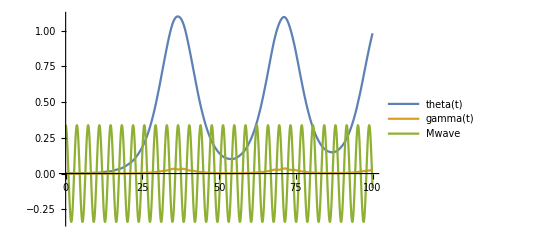

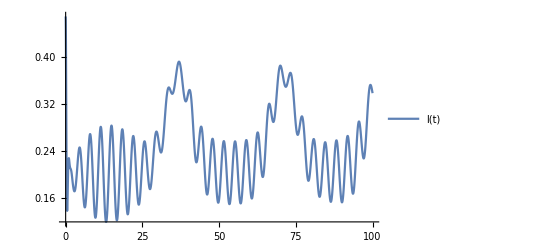

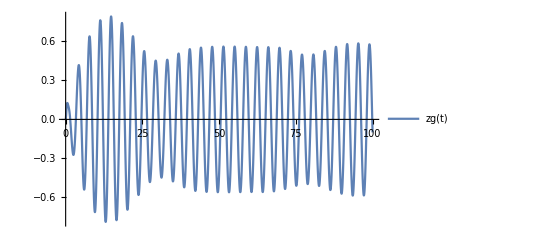

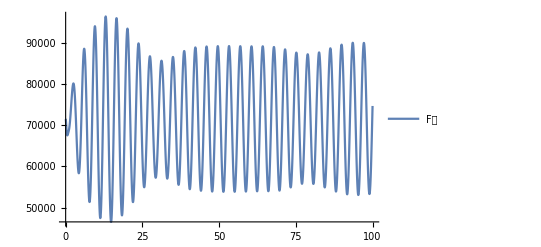

```mathematica
Plot[{th[t]/.s,ga[t]/.s,Mwave[t]/5000},{t,start,stop},PlotLegends->{"theta(t)","gamma(t)","Mwave"}]
Plot[l[t]/.s,{t,start,stop},PlotLegends->{"l(t)"}]
Plot[zg[t]/.s,{t,start,stop},PlotLegends->{"zg(t)"}]
Plot[Fj[t]/.s,{t,0,stop},PlotLegends->{"F浮"}]
```

## 第4题

```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=2433;
(*弹簧劲度系数*)
k=80000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=528.5018;
(*纵摇附加转动惯量*)
I0=7142.493;
(*纵摇激励力矩振幅*)
L=2140;
(*入射波浪频率*)
w=1.9806;
(*垂荡激励力振幅*)
f=1760;
(*浮子转动惯量*)
(*Ia=300*4866/(7π+(Sqrt[41]π)/5)*(Integrate[1/0.8*2*Pi*(r+(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5),-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8}]+Integrate[2*Pi*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+3.8}]+Integrate[2*Pi*(3.8-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))^2+a^2,{a,0,0.5}]);*)
Ia=8399.2;

(*垂荡附加质量*)
m0=1091.099;
(*纵摇兴波阻尼力矩系数*)
cr0=1655.909;
(*纵摇静水恢复力矩系数*)
Mrec=8890.7;
(*海水密度*)
rho=1025;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=(7.120975609756098-Pi*zg[t])*rho*g;
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
(*Ib[t_]:=258.149+774.448l[t]+1548.9l[t]^2;*)
(*Ib[t_]:=MomentOfInertia[Cylinder[{{0,0,0},{0.5,0,0}},0.5],{l[t]+0.5,0,0},{0,0,1}]*)
Ib[t_]:=m/12*(4*0.5^2-12*0.5*(0.5+l[t])+3*1^2+12*(0.5+l[t])^2)
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_,c_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_,crot_]:=-krot*ga[t]-crot*ga'[t];

start=300;
stop=start+10;
dim=1;
```

```mathematica
P4[c_,crot_]:=Sum[(c*(l'[t]^2)+crot*(ga'[t]^2))*dim,{t,start,stop,dim}]/.NDSolve[{m*xp''[t]==-Fpto[t,c]*Sin[th2[t]]+Fab[t]*Cos[th2[t]],m*zp''[t]==Fpto[t,c]*Cos[th2[t]]-m*g+Fab[t]*Sin[th2[t]],Ib[t]*th2''[t]==Mpto[t,crot]+Fab[t]*l[t],M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t,c]*Cos[th2[t]]-Fab[t]*Sin[th2[t]]-m0*zg''[t]-c0*zg'[t],Ia*th''[t]==Mwave[t]-Mpto[t,crot]+Fab[t]*d*Cos[th[t]]*Cos[th2[t]]-Fab[t]*d*Sin[th[t]]*Sin[th2[t]]-I0*th''[t]-cr0*th'[t]-Mrec*th[t],th'[0]==th[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==0,l[0]==l0-m/k,zg[0]==0},{th,ga,zg,l},{t,start,stop}]
```

```mathematica
First[P4[10000,1000]]
```

NDSolve::pdord: 某些函数的微分阶数为零，因此方程将作为微分代数方程组求解.

751.564

```mathematica
CalcP4[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Parallelize[Table[{pe,ppk,First[P4[ppk,pe]]},{ppk,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{pe,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]]
```

```mathematica
s=CalcP4[0,100000,6,0,100000,6]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

{{{0,0,0},{50000/3,0,11.157},{100000/3,0,20.7742},{50000,0,28.1501},{200000/3,0,33.2},{250000/3,0,36.225},{100000,0,37.6802}},{{0,50000/3,1149.34},{50000/3,50000/3,1155.93},{100000/3,50000/3,1160.01},{50000,50000/3,1161.59},{200000/3,50000/3,1161.15},{250000/3,50000/3,1159.34},{100000,50000/3,1156.74}},{{0,100000/3,1662.63},{50000/3,100000/3,1665.94},{100000/3,100000/3,1666.86},{50000,100000/3,1665.63},{200000/3,100000/3,1662.91},{250000/3,100000/3,1659.38},{100000,100000/3,1655.57}},{{0,50000,1709.73},{50000/3,50000,1711.92},{100000/3,50000,1712.05},{50000,50000,1710.36},{200000/3,50000,1707.47},{250000/3,50000,1704.},{100000,50000,1700.4}},{{0,200000/3,1585.1},{50000/3,200000/3,1587.14},{100000/3,200000/3,1587.39},{50000,200000/3,1586.01},{200000/3,200000/3,1583.55},{250000/3,200000/3,1580.57},{100000,200000/3,1577.47}},{{0,250000/3,1424.98},{50000/3,250000/3,1427.17},{100000/3,250000/3,1427.75},{50000,250000/3,1426.8},{200000/3,250000/3,1424.82},{250000/3,250000/3,1422.32},{100000,250000/3,1419.69}},{{0,100000,1273.76},{50000/3,100000,1276.14},{100000/3,100000,1277.04},{50000,100000,1276.48},{200000/3,100000,1274.91},{250000/3,100000,1272.82},{100000,100000,1270.55}}}

{0.,0.,0.} | {16666.7,0.,11.157} | {33333.3,0.,20.7742} | {50000.,0.,28.1501} | {66666.7,0.,33.2} | {83333.3,0.,36.225} | {100000.,0.,37.6802}
{0.,16666.7,1149.34} | {16666.7,16666.7,1155.93} | {33333.3,16666.7,1160.01} | {50000.,16666.7,1161.59} | {66666.7,16666.7,1161.15} | {83333.3,16666.7,1159.34} | {100000.,16666.7,1156.74}
{0.,33333.3,1662.63} | {16666.7,33333.3,1665.94} | {33333.3,33333.3,1666.86} | {50000.,33333.3,1665.63} | {66666.7,33333.3,1662.91} | {83333.3,33333.3,1659.38} | {100000.,33333.3,1655.57}
{0.,50000.,1709.73} | {16666.7,50000.,1711.92} | {33333.3,50000.,1712.05} | {50000.,50000.,1710.36} | {66666.7,50000.,1707.47} | {83333.3,50000.,1704.} | {100000.,50000.,1700.4}
{0.,66666.7,1585.1} | {16666.7,66666.7,1587.14} | {33333.3,66666.7,1587.39} | {50000.,66666.7,1586.01} | {66666.7,66666.7,1583.55} | {83333.3,66666.7,1580.57} | {100000.,66666.7,1577.47}
{0.,83333.3,1424.98} | {16666.7,83333.3,1427.17} | {33333.3,83333.3,1427.75} | {50000.,83333.3,1426.8} | {66666.7,83333.3,1424.82} | {83333.3,83333.3,1422.32} | {100000.,83333.3,1419.69}
{0.,100000.,1273.76} | {16666.7,100000.,1276.14} | {33333.3,100000.,1277.04} | {50000.,100000.,1276.48} | {66666.7,100000.,1274.91} | {83333.3,100000.,1272.82} | {100000.,100000.,1270.55}

{{0,0,0},{50000/3,0,11.157},{100000/3,0,20.7742},{50000,0,28.1501},{200000/3,0,33.2},{250000/3,0,36.225},{100000,0,37.6802},{0,50000/3,1149.34},{50000/3,50000/3,1155.93},{100000/3,50000/3,1160.01},{50000,50000/3,1161.59},{200000/3,50000/3,1161.15},{250000/3,50000/3,1159.34},{100000,50000/3,1156.74},{0,100000/3,1662.63},{50000/3,100000/3,1665.94},{100000/3,100000/3,1666.86},{50000,100000/3,1665.63},{200000/3,100000/3,1662.91},{250000/3,100000/3,1659.38},{100000,100000/3,1655.57},{0,50000,1709.73},{50000/3,50000,1711.92},{100000/3,50000,1712.05},{50000,50000,1710.36},{200000/3,50000,1707.47},{250000/3,50000,1704.},{100000,50000,1700.4},{0,200000/3,1585.1},{50000/3,200000/3,1587.14},{100000/3,200000/3,1587.39},{50000,200000/3,1586.01},{200000/3,200000/3,1583.55},{250000/3,200000/3,1580.57},{100000,200000/3,1577.47},{0,250000/3,1424.98},{50000/3,250000/3,1427.17},{100000/3,250000/3,1427.75},{50000,250000/3,1426.8},{200000/3,250000/3,1424.82},{250000/3,250000/3,1422.32},{100000,250000/3,1419.69},{0,100000,1273.76},{50000/3,100000,1276.14},{100000/3,100000,1277.04},{50000,100000,1276.48},{200000/3,100000,1274.91},{250000/3,100000,1272.82},{100000,100000,1270.55}}

-Graphics3D-

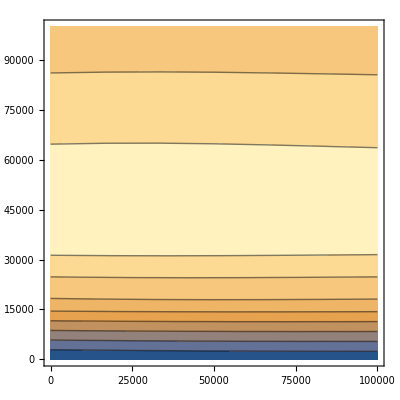

```mathematica
Grid[N[s],Frame->All]
ss=Flatten[s,1]
ListPlot3D[ss]
ListContourPlot[ss]
```

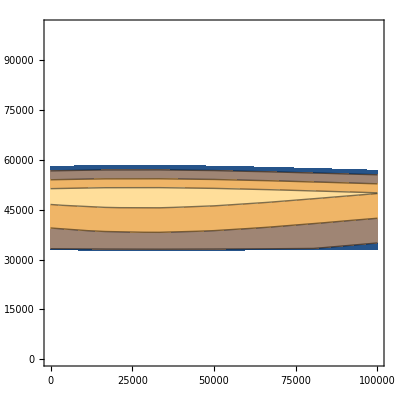

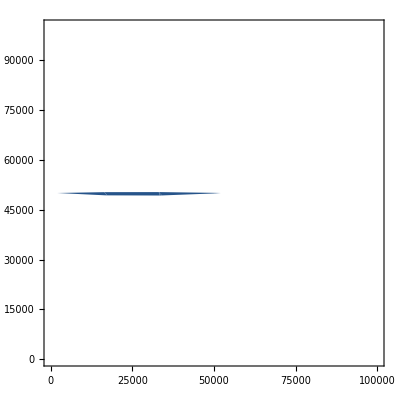

```mathematica
ListContourPlot[ss,PlotRange->{1650,1800}]
ListContourPlot[ss,PlotRange->{1710,1800}]
```